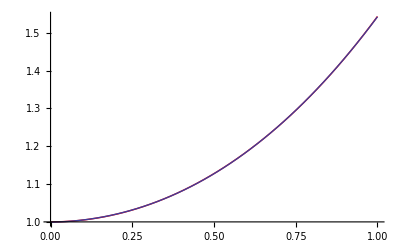

Погрешность приближения равна: 0.000226351

```mathematica
(*Зададим данную функцию*)
f[x_]=Cosh[x];
(*Зададим отрезок аппроксимации*)
a=0;
b=1;
(*Зададим количество функций в семействе*)
n=3;
(*Зададим семейство алгебраических многочленов*)
F=Table[x^k,{k,0,n}];
(*Построим матрицу Грамма*)MGr=Table[Integrate[F[[i]]*F[[j]],{x,a,b}],{i,1,n+1},{j,1,n+1}];
(*Зададим столбец свободных членов системы уравнений*)
B=Table[Integrate[f[x]*F[[i]],{x,a,b}],{i,1,n+1}];
(*Найдем коэффициенты многочлена наилучших среднеквадратических приближений*)
K=Inverse[MGr].B;
(*Построим многочлен наилучшего среднеквадратического приближения*)
phi[x_]=K.F;
(*Построим графики исходной функции и найденного обобщенного многочлена в одной системе координат*)
G=Plot[f[x],{x,a,b},PlotStyle->Red];
GPhi=Plot[phi[x],{x,a,b}];
Show[G,GPhi]
r=Sqrt[NIntegrate[(f[x]-phi[x])^2,{x,a,b}]];
Print["Погрешность приближения равна: ",r]
```